## Import

```mathematica
SetDirectory[""](*Set to directory of results*)
```

```mathematica
filename="quiver1";
```

```mathematica
file=Import[filename]
```

{/P10_z6/Eint,/P10_z6/Lint,/P10_z6/sols,/P10_z2/Eint,/P10_z2/Lint,/P10_z2/sols,/P10_z8/Lint,/P10_z8/Eint,/P10_z8/sols,/P_list,/P10_z4/Lint,/P10_z4/Eint,/P10_z4/sols,/zstar_list,/P10_z5/Lint,/P10_z5/Eint,/P10_z5/sols}

## LE plot

```mathematica
P=10;
zstar=2;
```

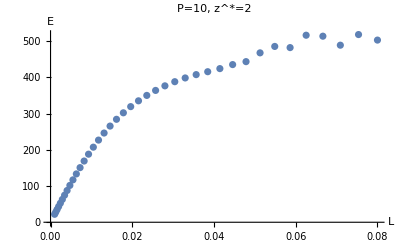

```mathematica
EE=Import[filename,"P"<>ToString[P]<>"_z"<>ToString[zstar]<>"/Eint"];
LL=Import[filename,"P"<>ToString[P]<>"_z"<>ToString[zstar]<>"/Lint"];
ListPlot[Transpose[{LL,EE}],AxesLabel->{"L","E"},PlotLabel->"P="<>ToString[P]<>", z^*="<>ToString[zstar]]
```

## Shape of string

```mathematica
i=30; (*index of the single string to be plotted*)
P=10;
zstar=2;
```

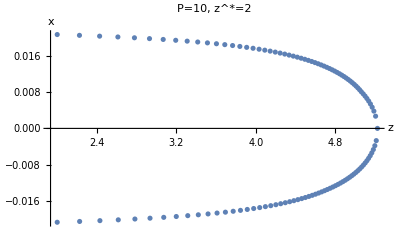

```mathematica
sols=Import[filename,"P"<>ToString[P]<>"_z"<>ToString[zstar]<>"/sols"];
LL=Import[filename,"P"<>ToString[P]<>"_z"<>ToString[zstar]<>"/Lint"];
II=Sqrt[Array[#&,IntegerPart[Length[sols[[Length[sols]/2+1;;-1,i]]]/2+.5],{0,(LL[[i]]/2)^2}]];
II=DeleteDuplicates[Sort[Join[-II,II]]];
ListPlot[Transpose[{sols[[Length[sols]/2+1;;-1,i]],II}],AxesLabel->{"z","x"},PlotLabel->"P="<>ToString[P]<>", z^*="<>ToString[zstar]]
```